Define everything in one place.

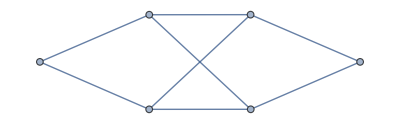

```mathematica
SetDirectory["~/Documents/UNH/Research/code/OTimes/sp4/"];
Clear[GammaAdj, GammaSymb, q, rho,n, dim, lvl, braid];
GammaAdj = { 
{0,1,1,0,0,0},
{1,0,0,1,1,0},
{1,0,0,1,1,0}, 
{0,1,1,0,0,1},
{0,1,1,0,0,1},
{0,0,0,1,1,0} 
};
AdjacencyGraph[ GammaAdj] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo, pp];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo, pp];
GammaSymb = { 
{0,aa,bb,0,0,0},
{cc,0,0,dd,ee,0},
{ff,0,0,gg,hh,0}, 
{0,ii,jj,0,0,kk},
{0,ll,mm,0,0,nn},
{0,0,0,oo,pp,0}
};
quan[n_, qew_]:=(qew^n-qew^-n)/(qew-qew^-1);
inDeg[z_]:=360(z//Arg)/(2Pi)//N
dim=2;
lvl = 3;
q=AlgebraicNumber"0.966"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-1339947038318497824042054379340224188424396116226678218098746796796408746191132980696413338764113250280671161186017258829796639550661461533832401727/2370999073893603146083203759119869452862559369549759692155537072171686985346145191498188014223753818764622191973847070734180294896688571062539863872,«30»,-98245651314592044693777734500129325005915455945333252338214360185670145735558898777861037554864301452324901754188480255969981454903597/74093721059175098315100117472495920401954980298429990379860533505365218292067037234318375444492306836394443499182720960443134215521517845704370746}]0.9659258262890683;
oldq = Exp[(2Pi I)/(4(dim+lvl+1))];
rho = q^5; (* should this be -q^5??? *)

Hom0to2 = GetHomBasisList[GammaSymb, 0,2];
Hom0to0 = GetHomBasisList[GammaSymb,0,0];
Hom1to1 = GetHomBasisList[GammaSymb,1,1];
Hom2to4 = GetHomBasisList[GammaSymb, 2,4];
Hom2to3 = GetHomBasisList[GammaSymb, 2,3];
Hom2to2 = GetHomBasisList[GammaSymb,2,2];
Hom2to1 = GetHomBasisList[GammaSymb,2,1];
Hom2to0 = GetHomBasisList[GammaSymb,2,0];
Hom1to2 = GetHomBasisList[GammaSymb,1,2];
Hom1to1 = GetHomBasisList[GammaSymb,1,1];
Hom1to0 = GetHomBasisList[GammaSymb,1,0];
Hom0to1 = GetHomBasisList[GammaSymb,0,1];
Hom0to0 = GetHomBasisList[GammaSymb,0,0];
Hom0to2 = GetHomBasisList[GammaSymb, 0,2];
Hom3to3 = GetHomBasisList[GammaSymb, 3,3];
Cap = GenerateCap[GammaAdj, GammaSymb];
Cup = InTermsOf[Dagger[Cap], Hom0to2];
Cup = ScaleByConstant[Cup, -1];
Stick = GenerateStick[GammaAdj, GammaSymb];
DoubleStick = InTermsOf[BigTens[Stick, Stick], Hom2to2];

braidSol = {Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738,Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,1/2,1,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6),1/4 (-1+√3),1+√3,Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"-0.448"+"0.259" ⅈRoot[1-4 #1^2+15 #1^4-4 #1^6+#1^8&,4]-0.4482877360840268,-√(-1+√3),-√(2 (1+√3)),-1/2 √(-1+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,√(2+√3),Root"-0.157"Root[-1+40 #1^2+32 #1^4&,1]-0.15658560865650772,(√(2-√3))/2,Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,-1/(√2),-1/(√2),1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),((1/2+ⅈ/2) ((-2+ⅈ)+√3))/(√2),-1/2 √(-1+√3),Root"-0.157"Root[-1+40 #1^2+32 #1^4&,1]-0.15658560865650772,-√(-1+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,(√(2-√3))/2,-√(2 (1+√3)),√(2+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,(√(2-√3))/2,√(2+√3),1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6),1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),1,1/2,1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6),Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,1/4 (√2-√6),√(1/2 (-1+√3)),-√(2+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,-√(1+√3),√(1/2 (-1+√3)),-1/2 √(-5+3 √3),Root"-0.448"+"0.259" ⅈRoot[1-4 #1^2+15 #1^4-4 #1^6+#1^8&,4]-0.4482877360840268,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,1+√3,1/4 (-1+√3),1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,-√(2+√3),√(1/2 (-1+√3)),1/4 (√2-√6),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,-1/2 √(-5+3 √3),√(1/2 (-1+√3)),-√(1+√3),(ⅈ-√3)/(√2+√6),Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,-1/(√2),-1/(√2),Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),√(2+√3),(√(2-√3))/2,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738};
braid = Hom2to2;
For[i=1,i<=Length[Hom2to2],i++,
braid[[i]][["scalar"]] = braidSol[[i]]
];
braid = braid//GPARootReduce;
```

```mathematica
Cap = {<|"scalar"->AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->aa**cc,"q"->1,"s"->1,"t"->1|>,<|"scalar"->AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->bb**ff,"q"->1,"s"->1,"t"->1|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->cc**aa,"q"->2,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->dd**ii,"q"->2,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->ee**ll,"q"->2,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->ff**bb,"q"->3,"s"->3,"t"->3|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->gg**jj,"q"->3,"s"->3,"t"->3|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->hh**mm,"q"->3,"s"->3,"t"->3|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->ii**dd,"q"->4,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->jj**gg,"q"->4,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->kk**oo,"q"->4,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->ll**ee,"q"->5,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->mm**hh,"q"->5,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->nn**pp,"q"->5,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->oo**kk,"q"->6,"s"->6,"t"->6|>,<|"scalar"->-AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->pp**nn,"q"->6,"s"->6,"t"->6|>};
Cup = {<|"scalar"->AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->1,"q"->aa**cc,"s"->1,"t"->1|>,<|"scalar"->AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->1,"q"->bb**ff,"s"->1,"t"->1|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->2,"q"->cc**aa,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->2,"q"->dd**ii,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->2,"q"->ee**ll,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->3,"q"->ff**bb,"s"->3,"t"->3|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->3,"q"->gg**jj,"s"->3,"t"->3|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->3,"q"->hh**mm,"s"->3,"t"->3|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->4,"q"->ii**dd,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->4,"q"->jj**gg,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->4,"q"->kk**oo,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->5,"q"->ll**ee,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->5,"q"->mm**hh,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->5,"q"->nn**pp,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->6,"q"->oo**kk,"s"->6,"t"->6|>,<|"scalar"->-AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->6,"q"->pp**nn,"s"->6,"t"->6|>};
```